```mathematica
(*Mathematica*)
```

```mathematica
Clear[f,g,h,k,s0,ff,ll,kk,mm,a,g3,ga,x,y,w]
```

```mathematica
(*Fourier Square Wave function*)
```

```mathematica
ff[x_]:=1/2+(ⅈ (ArcTanh[ⅇ^(-7 ⅈ π *Mod[x,1])]-ArcTanh[ⅇ^(7 ⅈ π *Mod[x,1])]))/π
```

```mathematica
(*Pi/2 phased function*)
```

```mathematica
gg[x_]:=ff[x+Pi/2]
```

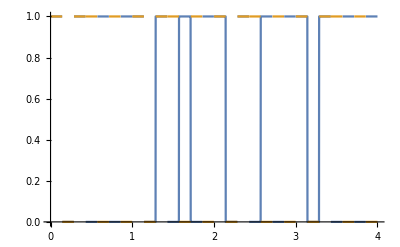

```mathematica
Plot[{ff[x],gg[x]},{x,0,4}]
```

```mathematica
s0=N[Log[2]/Log[5]];
```

```mathematica
(*four phased functions*)
```

```mathematica
kk[x_]=N[Re[Sum[ff[5^k*x]/5^(s0*k),{k,0,20}]]];
ll[x_]=N[Re[Sum[gg[5^k*(x)]/5^(s0*k),{k,0,20}]]];
```

```mathematica
nn[x_]=N[Re[Sum[ff[5^k*x+1/2]/5^(s0*k),{k,0,20}]]];
mm[x_]=N[Re[Sum[gg[5^k*(x)+1/2]/5^(s0*k),{k,0,20}]]];
```

```mathematica
n0=1000000;
a=Union[ParallelTable[{ll[t],kk[t]},{t,0,1,1/n0}]];
```

```mathematica
b=Union[ParallelTable[{ll[t],nn[t]},{t,0,1,1/n0}]];
```

```mathematica
c=Union[ParallelTable[{kk[t],mm[t]},{t,0,1,1/n0}]];
```

```mathematica
d=Union[ParallelTable[{nn[t],mm[t]},{t,0,1,1/n0}]];
```

```mathematica
g[1]=ListPlot[a,PlotRange->All,AspectRatio->Automatic,Axes->False,PlotStyle->PointSize[0.002],ImageSize->2000,ColorFunction->Hue];
```

```mathematica
g[2]=ListPlot[b,PlotRange->All,AspectRatio->Automatic,Axes->False,PlotStyle->PointSize[0.002],ImageSize->2000,ColorFunction->Hue];
```

```mathematica
g[3]=ListPlot[c,PlotRange->All,AspectRatio->Automatic,Axes->False,PlotStyle->PointSize[0.002],ImageSize->2000,ColorFunction->Hue];
```

```mathematica
g[4]=ListPlot[d,PlotRange->All,AspectRatio->Automatic,Axes->False,PlotStyle->PointSize[0.002],ImageSize->2000,ColorFunction->Hue];
```

```mathematica
Export["biscuit_SquareWave_2ndKind_1000000_g1.jpg",g[1]]
Export["biscuit_SquareWave_2ndKind_1000000_g2.jpg",g[2]]
Export["biscuit_SquareWave_2ndKind_1000000_g3.jpg",g[3]]
Export["biscuit_SquareWave_2ndKind_1000000_g4.jpg",g[4]]
```

biscuit_SquareWave_2ndKind_1000000_g1.jpg

biscuit_SquareWave_2ndKind_1000000_g2.jpg

biscuit_SquareWave_2ndKind_1000000_g3.jpg

biscuit_SquareWave_2ndKind_1000000_g4.jpg

```mathematica
(*end*)
```